Positron energy distribution in a factorized trident process

A. I. Titov, U. Hernandez Acosta, and B. Kämpfer, Phys Rev A 104, 062811 (2021)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

```mathematica
Clear[ℏ,c,ωeV]
ℏ=1.05 10^-34;(*[Js]*)
c=3 10^8;(*[m/s]*)
ωeV=1.55;(*[eV] laser photon energy *)
(2π c)/(ωeV e/ℏ)10^6(*[μm] wavelength ~800nm *)
```

0.798066

## Eq 7 asymptotic expression for Bessel function

(ⅇ^(-n (-√(1-z^2/n^2)+ArcTanh[√(1-z^2/n^2)])))/(√(2 π) √(n √(1-z^2/n^2)))

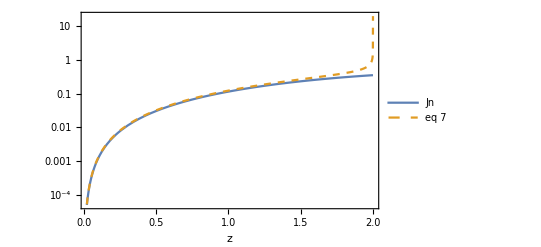

```mathematica
(* eq 7 asymptotic expression for Bessel function *)
(* this expression has 2 typos. the first power should be -1/2 and the argument of the exponent should not have the 2 factor. see for example Acosta_2021_New_J._Phys._23_095008 for the correct expression *)
Clear[Jnz7,n,z,a]
a=ArcTanh[Sqrt[1-z^2/n^2]];
Jnz7=(2π n Tanh[a])^(-1/2)Exp[-n(a-Tanh[a])]
D[Jnz7,z]//Simplify;
n=2;
LogPlot[{BesselJ[n,z],Jnz7},{z,n/100,n},Frame->True,FrameLabel->{"z",""},PlotLegends->{"Jn","eq 7"},PlotStyle->{Default,Dashed}]//Quiet
```

## Figure 1: nCS

Increase nmaxmin to have better match with paper

```mathematica
Clear[z,u,χ,α,m,e,Ee,w,dΓnlCdωeq8,ωp,C1,Jnzeq7,dJnzeq7,Fneq3,Fneq7,uneq6,zeq5,nmaxmin]
Clear[Fig1aξ1full,Fig1aξ3full,Fig1aξ10full,Fig1aξ1,Fig1aξ3,Fig1aξ10,Fig1bξ1full,Fig1bξ3full,Fig1bξ10full,Fig1bξ1,Fig1bξ3,Fig1bξ10,Fig1cξ1full,Fig1cξ3full,Fig1cξ10full,Fig1cξ1,Fig1cξ3,Fig1cξ10]
```

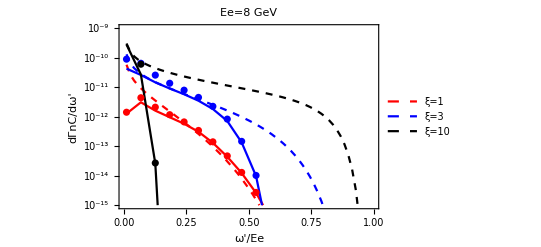

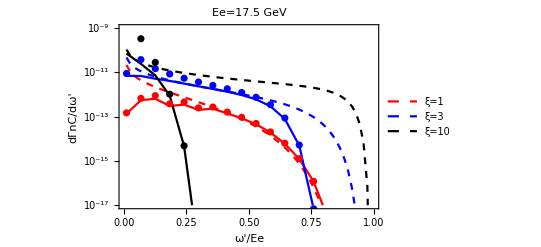

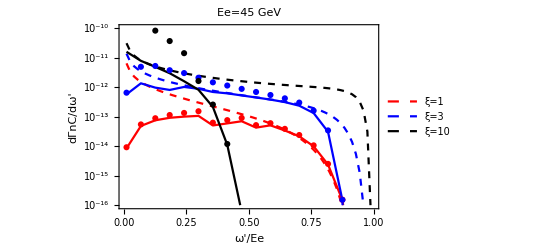

```mathematica
α=1/137;(*[]*)
m=9.1 10^-31;(*[Kg]*)
e=1.6 10^-19;(*[C]*)

(* number of harmonics to include *)
nmaxmin=30;

(* "global" multiplicative constant for normalization to match the figure in the paper *)
C1=10^33.9;(*[]*)

(* eq8: large -ξ approximation [34]*)
dΓnlCdωeq8[x_,ξ_,EeGeV_]:=Module[{z,u,w,ξs,χ,γe,Ee,ωpGeV},
ωpGeV=x EeGeV;

(* The laser frequency is chosen as ω=1.55 eV... 0.8μm *)
ξs=4.12 10^5 0.8;(*[]*)

γe=EeGeV/(0.511 10^-3);(* [] *)
Ee=EeGeV e 10^9;(*[J]*)

(* chi*)
χ=2 ξ γe/ξs;
 
(* eq 6 *)
u=ωpGeV/(EeGeV-ωpGeV);
(* eq 5 *)
z=(u/χ)^(2/3);
w=1+u^2/(2(1+u));

Return[-C1(α m^2)/Ee^2(NIntegrate[AiryAi[y],{y,z,∞}]+2/z w AiryAiPrime[z])]
]


(* eq3: includes full Bessel function (and its derivative) *)
Fneq3[z_,u_,ξ_,n_]:=-BesselJ[n,z]^2+ξ^2(1+u^2/(2(1+u)))((n^2/z^2-1)BesselJ[n,z]^2+(1/2 (BesselJ[-1+n,z]-BesselJ[1+n,z]))^2)

(* eq 6: auxiliary functions *)
uneq6[n_,χ_,ξ_]:=(2n χ)/(ξ(1+ξ^2));
zeq5[n_,χ_,ξ_,u_]:=(ξ^2 Sqrt[1+ξ^2])/χ Sqrt[u(uneq6[n,χ,ξ]-u)];

(* eq 2: rate with full Bessel functions *)
dΓnlCdωeq2[x_,ξ_,EeGeV_]:=Module[{nmin,sum,ωpGeV,ξs,γe,Ee,χ,u,ωGeV,mGeV},
ωpGeV=x EeGeV;
mGeV=0.511 10^-3;(*[GeV]*)
ωGeV=1.55 10^-9;(*[GeV]*)

(* The laser frequency is chosen as ω=1.55 eV... 0.8μm *)
ξs=4.12 10^5 0.8;(*[]*)

γe=EeGeV/(0.511 10^-3);(* [] *)
Ee=EeGeV e 10^9;(*[J]*)

(* chi*)
χ=2 ξ γe/ξs;

(* eq 6 *)
u=ωpGeV/(EeGeV-ωpGeV);

nmin=Ceiling[1+(mGeV^2(1+ξ^2)ωpGeV)/(4ωGeV EeGeV(EeGeV-ωpGeV))];

sum=Sum[Fneq3[zeq5[n,χ,ξ,u],u,ξ,n],{n,nmin,nmin+nmaxmin,1}];
Return[C1(α m^2)/Ee^2 sum]
]//Quiet


(* eq 7 *)
Jnzeq7[n_,z_]:=(ⅇ^(-n (-√(1-z^2/n^2)+ArcTanh[√(1-z^2/n^2)])))/(√(2 π) √(n √(1-z^2/n^2)))
dJnzeq7[n_,z_]:=(ⅇ^(n √(1-z^2/n^2)-n ArcTanh[√(1-z^2/n^2)]) (2 n^3 √(1-z^2/n^2)+z^2 (1-2 n √(1-z^2/n^2))))/(2 √(2 π) z (n^2-z^2) √(n √(1-z^2/n^2)))

(* eq3 using approximation from eq 7 *)
Fneq7[z_,u_,ξ_,n_]:=-Jnzeq7[n,z]^2+ξ^2(1+u^2/(2(1+u)))((n^2/z^2-1)Jnzeq7[n,z]^2+dJnzeq7[n,z]^2)


dΓnlCdωeq7[x_,ξ_,EeGeV_]:=Module[{nmin,sum,ωpGeV,ξs,γe,Ee,χ,u,ωGeV,mGeV},
ωpGeV=x EeGeV;
mGeV=0.511 10^-3;(*[GeV]*)
ωGeV=1.55 10^-9;(*[GeV]*)

(* The laser frequency is chosen as ω=1.55 eV... 0.8μm *)
ξs=4.12 10^5 0.8;(*[]*)

γe=EeGeV/(0.511 10^-3);(* [] *)
Ee=EeGeV e 10^9;(*[J]*)

(* chi*)
χ=2 ξ γe/ξs;

(* eq 6 *)
u=ωpGeV/(EeGeV-ωpGeV);

nmin=Ceiling[1+(mGeV^2(1+ξ^2)ωpGeV)/(4ωGeV EeGeV(EeGeV-ωpGeV))];

sum=Sum[Fneq7[zeq5[n,χ,ξ,u],u,ξ,n],{n,nmin,nmin+nmaxmin,1}];
Return[C1(α m^2)/Ee^2 sum]
]//Quiet



xmin=0.01;
xmax=0.99;
xdim=18;

(*a*)
Fig1aξ1full=ParallelTable[{x,dΓnlCdωeq2[x,1,8]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1aξ3full=ParallelTable[{x,dΓnlCdωeq2[x,3,8]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1aξ10full=ParallelTable[{x,dΓnlCdωeq2[x,10,8]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1aξ1=ParallelTable[{x,dΓnlCdωeq7[x,1,8]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1aξ3=ParallelTable[{x,dΓnlCdωeq7[x,3,8]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1aξ10=ParallelTable[{x,dΓnlCdωeq7[x,10,8]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];

(*b*)
Fig1bξ1full=ParallelTable[{x,dΓnlCdωeq2[x,1,17.5]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1bξ3full=ParallelTable[{x,dΓnlCdωeq2[x,3,17.5]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1bξ10full=ParallelTable[{x,dΓnlCdωeq2[x,10,17.5]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1bξ1=ParallelTable[{x,dΓnlCdωeq7[x,1,17.5]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1bξ3=ParallelTable[{x,dΓnlCdωeq7[x,3,17.5]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1bξ10=ParallelTable[{x,dΓnlCdωeq7[x,10,17.5]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];

(*c*)
Fig1cξ1full=ParallelTable[{x,dΓnlCdωeq2[x,1,45]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1cξ3full=ParallelTable[{x,dΓnlCdωeq2[x,3,45]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1cξ10full=ParallelTable[{x,dΓnlCdωeq2[x,10,45]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1cξ1=ParallelTable[{x,dΓnlCdωeq7[x,1,45]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1cξ3=ParallelTable[{x,dΓnlCdωeq7[x,3,45]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];
Fig1cξ10=ParallelTable[{x,dΓnlCdωeq7[x,10,45]},{x,xmin,xmax,(xmax-xmin)/(xdim-1)}];

Show[{LogPlot[{dΓnlCdωeq8[x,1,8],dΓnlCdωeq8[x,3,8],dΓnlCdωeq8[x,10,8]},{x,0.01,0.99},Frame->True,FrameLabel->{"ω'/Ee","dΓnC/dω'"},PlotLegends->{"ξ=1","ξ=3","ξ=10"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed}},PlotLabel->"Ee=8 GeV",PlotPoints->2,PlotRange->{{0,1},{10^-15,10^-9}}],
ListLogPlot[{Fig1aξ1full,Fig1aξ3full,Fig1aξ10full},Frame->True,FrameLabel->{"ω'/Ee","dΓnC/dω'"},Joined->True,PlotStyle->{{Red},{Blue},{Black}},PlotLabel->"Ee=8 GeV",PlotRange->{10^-15,10^-9}],
ListLogPlot[{Fig1aξ1,Fig1aξ3,Fig1aξ10},Frame->True,FrameLabel->{"ω'/Ee","dΓnC/dω'"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed}},PlotLabel->"Ee=8 GeV",PlotRange->{10^-15,10^-9}]
}]

Show[{LogPlot[{dΓnlCdωeq8[x,1,17.5],dΓnlCdωeq8[x,3,17.5],dΓnlCdωeq8[x,10,17.5]},{x,0.01,0.99},Frame->True,FrameLabel->{"ω'/Ee","dΓnC/dω'"},PlotLegends->{"ξ=1","ξ=3","ξ=10"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed}},PlotLabel->"Ee=17.5 GeV",PlotPoints->2,PlotRange->{{0,1},{10^-17,10^-9}}],
ListLogPlot[{Fig1bξ1full,Fig1bξ3full,Fig1bξ10full},Frame->True,FrameLabel->{"ω'/Ee","dΓnC/dω'"},Joined->True,PlotStyle->{{Red},{Blue},{Black}},PlotLabel->"Ee=17.5 GeV",PlotRange->{10^-17,10^-9}],
ListLogPlot[{Fig1bξ1,Fig1bξ3,Fig1bξ10},Frame->True,FrameLabel->{"ω'/Ee","dΓnC/dω'"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed}},PlotLabel->"Ee=17.5 GeV",PlotRange->{10^-17,10^-9}]
}]

Show[{LogPlot[{dΓnlCdωeq8[x,1,45],dΓnlCdωeq8[x,3,45],dΓnlCdωeq8[x,10,45]},{x,0.01,0.99},Frame->True,FrameLabel->{"ω'/Ee","dΓnC/dω'"},PlotLegends->{"ξ=1","ξ=3","ξ=10"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed}},PlotLabel->"Ee=45 GeV",PlotPoints->2,PlotRange->{{0,1},{10^-16,10^-10}}],
ListLogPlot[{Fig1cξ1full,Fig1cξ3full,Fig1cξ10full},Frame->True,FrameLabel->{"ω'/Ee","dΓnC/dω'"},Joined->True,PlotStyle->{{Red},{Blue},{Black}},PlotLabel->"Ee=45 GeV",PlotRange->{10^-16,10^-10}],
ListLogPlot[{Fig1cξ1,Fig1cξ3,Fig1cξ10},Frame->True,FrameLabel->{"ω'/Ee","dΓnC/dω'"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed}},PlotLabel->"Ee=45 GeV",PlotRange->{10^-16,10^-10}]
}]
```

## Eq 14 auxiliary function using approximation to Bessel function

```mathematica
(* because the aproximation in equation 7 has a typo, equation 14 does not match the expansion applied to equation 10 *)
Clear[Jnz7,dJnz7,𝒥n,n,z,a,ξ]
a=ArcTanh[Sqrt[1-z^2/n^2]];
Jnz7=(2π n Tanh[a])^(-1/2)Exp[-n(a-Tanh[a])];
dJnz7=D[Jnz7,z]//Simplify;
𝒥n=(Jnz7^2+ξ^2(2u-1)((n^2/z^2-1)Jnz7^2+dJnz7^2))//FullSimplify
```

(ⅇ^(2 n √(1-z^2/n^2)-2 n ArcTanh[√(1-z^2/n^2)]) (4 (-n^2 z+z^3)^2+(-1+2 u) (8 n^6-24 n^4 z^2+z^4+24 n^2 z^4-8 z^6+4 n^3 z^2 √(1-z^2/n^2)-4 n z^4 √(1-z^2/n^2)) ξ^2))/(8 n π z^2 (n^2-z^2)^2 √(1-z^2/n^2))

## Figure 2: nBW

For “fixed positron energy E+ = Ee/2”

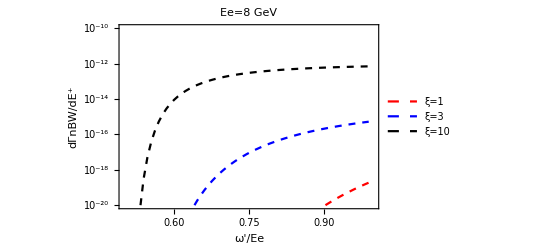

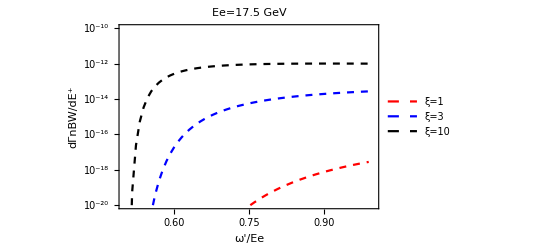

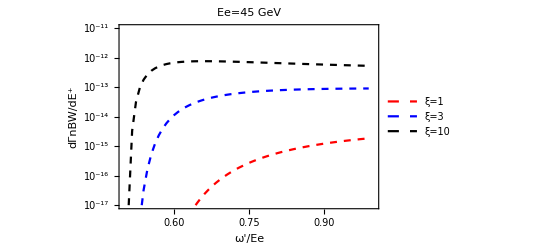

```mathematica
Clear[z,u,χ,α,m,e,Ee,w,dΓnlBWdωeq15,ωp,C1,Jnzeq7,dJnzeq7,Fneq3,Fneq7,uneq6,zeq5,dΓnlBWdEeq9,mGeV]
Clear[Fig2aξ1full,Fig2aξ3full,Fig2aξ10full,Fig2aξ1,Fig2aξ3,Fig2aξ10,Fig2bξ1full,Fig2bξ3full,Fig2bξ10full,Fig2bξ1,Fig2bξ3,Fig2bξ10,Fig2cξ1full,Fig2cξ3full,Fig2cξ10full,Fig2cξ1,Fig2cξ3,Fig2cξ10,𝒥neq10,zeq12,uneq13]

α=1/137;(*[]*)
m=9.1 10^-31;(*[Kg]*)
e=1.6 10^-19;(*[C]*)

(* number of harmonics to include *)
nmaxmin=3;

C1=10^33.9;(*[]*)

(* large -ξ approximation *)
dΓnlBWdωeq15[x_,ξ_,EeGeV_]:=Module[{z,u,w,ξs,χγ,γe,Ee,ωpGeV,Ep,ωp,EpGeV,γγ},
ωpGeV=x EeGeV;(*[GeV]*)
ωp=ωpGeV e 10^9;(*[J]*)

(* fixed positron energy *)
EpGeV=EeGeV/2;(*[GeV]*)
Ep=EpGeV e 10^9;(*[J]*)

(* The laser frequency is chosen as ω=1.55 eV... 0.8μm *)
ξs=4.12 10^5 0.8;(*[]*)

γγ=ωpGeV/(0.511 10^-3);(* [] *)
γe=EeGeV/(0.511 10^-3);(* [] *)
Ee=EeGeV e 10^9;(*[J]*)

(* chi*)
χγ=2 ξ γγ/ξs;
 
(* eq 13 *)
u=ωpGeV^2/(4EpGeV(ωpGeV-EpGeV));(*[]*)

z=(4u/χγ)^(2/3);(*[]*)

Return[C1(α m^2)/ωp^2(NIntegrate[AiryAi[y],{y,z,∞}]-2/z(2u-1) AiryAiPrime[z])]
]//Quiet

LogPlot[{10^5 dΓnlBWdωeq15[x,1,8],dΓnlBWdωeq15[x,3,8],dΓnlBWdωeq15[x,10,8]},{x,0.501,0.99},Frame->True,FrameLabel->{"ω'/Ee","dΓnBW/dE^+"},PlotLegends->{"ξ=1","ξ=3","ξ=10"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed}},PlotLabel->"Ee=8 GeV",PlotPoints->2,PlotRange->{{0.5,1},{10^-20,10^-10}}]

LogPlot[{dΓnlBWdωeq15[x,1,17.5],dΓnlBWdωeq15[x,3,17.5],dΓnlBWdωeq15[x,10,17.5]},{x,0.501,0.99},Frame->True,FrameLabel->{"ω'/Ee","dΓnBW/dE^+"},PlotLegends->{"ξ=1","ξ=3","ξ=10"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed}},PlotLabel->"Ee=17.5 GeV",PlotPoints->2,PlotRange->{{0.5,1},{10^-20,10^-10}}]

LogPlot[{dΓnlBWdωeq15[x,1,45],dΓnlBWdωeq15[x,3,45],dΓnlBWdωeq15[x,10,45]},{x,0.501,0.99},Frame->True,FrameLabel->{"ω'/Ee","dΓnBW/dE^+"},PlotLegends->{"ξ=1","ξ=3","ξ=10"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black,Dashed}},PlotLabel->"Ee=45 GeV",PlotPoints->2,PlotRange->{{0.5,1},{10^-17,10^-11}}]
```